```mathematica
eq1=x^2*y''[x]+x*y'[x]+(x^2-n^2)*y[x]==0;
eq2=(1-x^2)*y''[x]-2x(y'[x])+n(n+1)y[x]==0;
DSolve[eq1,y[x],x]//Flatten
DSolve[eq2,y[x],x]//Flatten
```

{y[x]→BesselJ[n,x] C[1]+BesselY[n,x] C[2]}

{y[x]→C[1] LegendreP[n,x]+C[2] LegendreQ[n,x]}

```mathematica
eq3=y''[x]== 10 Sin[y[x]] Cos[x];
DSolve[eq3,y[x],x]
```

DSolve[y''[x]==10 Cos[x] Sin[y[x]],y[x],x]

InterpolatingFunction[…][x]

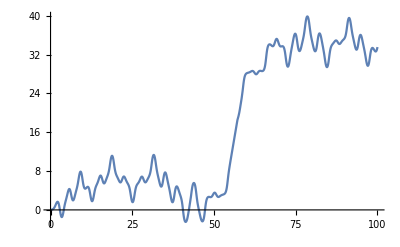

```mathematica
eq4=y'[x]== v[x] ;
eq5=v'[x]==10 Sin[y[x]]Cos[x];
sol=y[x]/.NDSolve[{eq4,eq5,y[0]==0,v[0]==0.1},y[x],{x,0,100}][[1]]
Plot[sol,{x,0,100}]
```